```mathematica
myblend:=Blend[{{1,Hue[0]},{t/3,Orange},{t/7,Yellow},{t/11,RGBColor[0.91,0.9,0.24]},{t/16,RGBColor[0.24, 0.92, 0.]},{t/24,RGBColor[0.33,0.96,1.]},{t/27,RGBColor[0.02, 0.53, 1.]},{t/32,RGBColor[0., 0., 0.84]},
{t/41,RGBColor[1., 0.02, 0.91]},{t/60,RGBColor[0.41000000000000003, 0.2, 0.65]},{t/200,RGBColor[0.31, 0., 0.33]}
,{1/10000,Black},{1/20000,RGBColor[0.71,0.71,0.71]},{0,White}},#]& /.t->0.5
n=1;{myblend[#],n++}&/@Flatten[{Table[1/n,{n,1,200}],0,1/20000}]
```

{{RGBColor[1., 0., 0.],1},{RGBColor[1., 0.3, 0.],2},{RGBColor[1., 0.4, 0.],3},{RGBColor[1., 0.45, 0.],4},{RGBColor[1., 0.48, 0.],5},{RGBColor[1., 0.5, 0.],6},{RGBColor[1., 0.625, 0.],7},{RGBColor[1., 0.71875, 0.],8},{RGBColor[1., 0.7916666666666667, 0.],9},{RGBColor[1., 0.85, 0.],10},{RGBColor[1., 0.8977272727272727, 0.],11},{RGBColor[1., 0.9375, 0.],12},{RGBColor[1., 0.9711538461538461, 0.],13},{RGBColor[1., 1., 0.],14},{RGBColor[0.9835, 0.9816666666666667, 0.043999999999999956],15},{RGBColor[0.9690625, 0.9656250000000001, 0.08249999999999996],16},{RGBColor[0.9563235294117647, 0.9514705882352942, 0.1164705882352941],17},{RGBColor[0.9450000000000001, 0.9388888888888889, 0.14666666666666667],18},{RGBColor[0.9348684210526316, 0.9276315789473685, 0.1736842105263158],19},{RGBColor[0.9257500000000001, 0.9175, 0.19799999999999995],20},{RGBColor[0.9175, 0.9083333333333333, 0.22000000000000003],21},{RGBColor[0.91, 0.9, 0.24],22},{RGBColor[0.8167826086956521, 0.9027826086956522, 0.20660869565217385],23},{RGBColor[0.7313333333333332, 0.9053333333333333, 0.17599999999999993],24},{RGBColor[0.65272, 0.90768, 0.14784],25},{RGBColor[0.5801538461538462, 0.9098461538461539, 0.12184615384615387],26},{RGBColor[0.5129629629629628, 0.9118518518518519, 0.09777777777777773],27},{RGBColor[0.45057142857142846, 0.9137142857142857, 0.07542857142857139],28},{RGBColor[0.3924827586206896, 0.915448275862069, 0.054620689655172396],29},{RGBColor[0.3382666666666666, 0.9170666666666667, 0.03519999999999999],30},{RGBColor[0.28754838709677416, 0.9185806451612903, 0.017032258064516113],31},{RGBColor[0.24, 0.92, 0.],32},{RGBColor[0.24818181818181817, 0.9236363636363637, 0.09090909090909083],33},{RGBColor[0.25588235294117645, 0.9270588235294118, 0.17647058823529416],34},{RGBColor[0.2631428571428571, 0.9302857142857143, 0.25714285714285723],35},{RGBColor[0.27, 0.9333333333333333, 0.3333333333333335],36},{RGBColor[0.2764864864864865, 0.9362162162162162, 0.40540540540540526],37},{RGBColor[0.28263157894736846, 0.9389473684210526, 0.47368421052631593],38},{RGBColor[0.2884615384615385, 0.9415384615384615, 0.5384615384615385],39},{RGBColor[0.294, 0.944, 0.5999999999999999],40},{RGBColor[0.2992682926829268, 0.9463414634146341, 0.6585365853658536],41},{RGBColor[0.3042857142857143, 0.9485714285714285, 0.7142857142857144],42},{RGBColor[0.3090697674418605, 0.9506976744186046, 0.7674418604651162],43},{RGBColor[0.31363636363636366, 0.9527272727272726, 0.818181818181818],44},{RGBColor[0.318, 0.9546666666666667, 0.8666666666666665],45},{RGBColor[0.32217391304347825, 0.9565217391304347, 0.9130434782608695],46},{RGBColor[0.3261702127659575, 0.9582978723404255, 0.9574468085106382],47},{RGBColor[0.33, 0.96, 1.],48},{RGBColor[0.27306122448979586, 0.8810204081632652, 1.],49},{RGBColor[0.2184000000000002, 0.8052000000000004, 1.],50},{RGBColor[0.1658823529411766, 0.7323529411764708, 1.],51},{RGBColor[0.11538461538461568, 0.6623076923076927, 1.],52},{RGBColor[0.06679245283018873, 0.5949056603773586, 1.],53},{RGBColor[0.02, 0.53, 1.],54},{RGBColor[0.017672727272727274, 0.4683272727272727, 0.9813818181818181],55},{RGBColor[0.015428571428571427, 0.4088571428571428, 0.9634285714285714],56},{RGBColor[0.01326315789473684, 0.35147368421052627, 0.9461052631578947],57},{RGBColor[0.01117241379310345, 0.29606896551724143, 0.9293793103448276],58},{RGBColor[0.009152542372881359, 0.242542372881356, 0.9132203389830509],59},{RGBColor[0.007200000000000001, 0.19080000000000003, 0.8976],60},{RGBColor[0.0053114754098360735, 0.14075409836065594, 0.8824918032786886],61},{RGBColor[0.0034838709677419335, 0.09232258064516125, 0.8678709677419354],62},{RGBColor[0.0017142857142857088, 0.045428571428571284, 0.8537142857142856],63},{RGBColor[0., 0., 0.84],64},{RGBColor[0.07008547008546984, 0.001401709401709396, 0.8449059829059828],65},{RGBColor[0.13804713804713786, 0.002760942760942759, 0.8496632996632997],66},{RGBColor[0.20398009950248763, 0.004079601990049753, 0.8542786069651741],67},{RGBColor[0.2679738562091504, 0.005359477124183007, 0.8587581699346405],68},{RGBColor[0.33011272141706927, 0.006602254428341383, 0.8631078904991948],69},{RGBColor[0.39047619047619064, 0.007809523809523813, 0.8673333333333333],70},{RGBColor[0.44913928012519555, 0.008982785602503911, 0.8714397496087637],71},{RGBColor[0.5061728395061731, 0.010123456790123463, 0.8754320987654322],72},{RGBColor[0.5616438356164386, 0.011232876712328773, 0.8793150684931507],73},{RGBColor[0.6156156156156154, 0.01231231231231231, 0.8830930930930931],74},{RGBColor[0.6681481481481479, 0.013362962962962958, 0.8867703703703703],75},{RGBColor[0.7192982456140353, 0.014385964912280707, 0.8903508771929824],76},{RGBColor[0.769119769119769, 0.01538239538239538, 0.8938383838383839],77},{RGBColor[0.8176638176638179, 0.01635327635327636, 0.8972364672364672],78},{RGBColor[0.8649789029535866, 0.017299578059071733, 0.900548523206751],79},{RGBColor[0.911111111111111, 0.01822222222222222, 0.9037777777777778],80},{RGBColor[0.956104252400549, 0.01912208504801098, 0.9069272976680385],81},{RGBColor[1., 0.02, 0.91],82},{RGBColor[0.9775523145212429, 0.02684844641724793, 0.9001077996195308],83},{RGBColor[0.9556390977443607, 0.03353383458646622, 0.8904511278195488],84},{RGBColor[0.9342414860681114, 0.040061919504643995, 0.8810216718266254],85},{RGBColor[0.9133414932680538, 0.04643818849449208, 0.8718115055079559],86},{RGBColor[0.8929219600725953, 0.0526678765880218, 0.8628130671506352],87},{RGBColor[0.8729665071770335, 0.058755980861244006, 0.8540191387559809],88},{RGBColor[0.8534594914251921, 0.06470727380248376, 0.8454228267297457],89},{RGBColor[0.8343859649122807, 0.07052631578947369, 0.8370175438596492],90},{RGBColor[0.8157316367842684, 0.0762174667437825, 0.8287969924812031],91},{RGBColor[0.797482837528604, 0.08178489702517165, 0.8207551487414187],92},{RGBColor[0.7796264855687607, 0.08723259762308995, 0.812886247877759],93},{RGBColor[0.7621500559910415, 0.0925643896976484, 0.8051847704367301],94},{RGBColor[0.7450415512465374, 0.09778393351800556, 0.797645429362881],95},{RGBColor[0.7282894736842105, 0.1028947368421053, 0.7902631578947368],96},{RGBColor[0.7118827997829625, 0.10790016277807923, 0.7830330982094411],97},{RGBColor[0.6958109559613318, 0.11280343716433947, 0.7759505907626207],98},{RGBColor[0.6800637958532697, 0.11760765550239231, 0.7690111642743223],99},{RGBColor[0.6646315789473685, 0.12231578947368421, 0.7622105263157896],100},{RGBColor[0.6495049504950495, 0.12693069306930693, 0.7555445544554455],101},{RGBColor[0.6346749226006192, 0.13145510835913315, 0.7490092879256967],102},{RGBColor[0.6201328564128767, 0.13589167092488508, 0.7426009197751661],103},{RGBColor[0.6058704453441297, 0.14024291497975708, 0.7363157894736843],104},{RGBColor[0.5918796992481204, 0.1445112781954887, 0.7301503759398498],105},{RGBColor[0.5781529294935451, 0.14869910625620658, 0.7241012909632571],106},{RGBColor[0.5646827348745695, 0.152808657156911, 0.718165272995573],107},{RGBColor[0.5514619883040935, 0.15684210526315792, 0.7123391812865497],108},{RGBColor[0.5384838242394979, 0.16080154514727182, 0.7066199903428296],109},{RGBColor[0.5257416267942583, 0.16468899521531102, 0.7010047846889952],110},{RGBColor[0.5132290184921764, 0.1685064011379801, 0.6954907539118066],111},{RGBColor[0.5009398496240601, 0.17225563909774438, 0.6900751879699248],112},{RGBColor[0.4888681881695389, 0.1759385188635305, 0.6847554727526781],113},{RGBColor[0.47700831024930745, 0.17955678670360115, 0.6795290858725762],114},{RGBColor[0.4653546910755149, 0.18311212814645308, 0.6743935926773456],115},{RGBColor[0.453901996370236, 0.18660617059891108, 0.6693466424682396],116},{RGBColor[0.4426450742240218, 0.19004048582995947, 0.6643859649122807],117},{RGBColor[0.4315789473684211, 0.19341659232827832, 0.6595093666369314],118},{RGBColor[0.4206988058381247, 0.1967359575409111, 0.6547147279964618],119},{RGBColor[0.41000000000000003, 0.2, 0.65],120},{RGBColor[0.40881936245572614, 0.1976387249114522, 0.6462219598583235],121},{RGBColor[0.40765807962529277, 0.1953161592505855, 0.6425058548009368],122},{RGBColor[0.40651567944250877, 0.19303135888501746, 0.638850174216028],123},{RGBColor[0.4053917050691245, 0.19078341013824887, 0.6352534562211982],124},{RGBColor[0.4042857142857143, 0.18857142857142858, 0.6317142857142857],125},{RGBColor[0.40319727891156465, 0.18639455782312925, 0.6282312925170068],126},{RGBColor[0.40212598425196855, 0.18425196850393702, 0.6248031496062992],127},{RGBColor[0.4010714285714286, 0.18214285714285716, 0.6214285714285714],128},{RGBColor[0.40003322259136215, 0.18006644518272427, 0.6181063122923588],129},{RGBColor[0.399010989010989, 0.17802197802197806, 0.6148351648351649],130},{RGBColor[0.3980043620501636, 0.1760087241003272, 0.6116139585605235],131},{RGBColor[0.39701298701298704, 0.17402597402597406, 0.6084415584415584],132},{RGBColor[0.39603651987110633, 0.17207303974221266, 0.6053168635875403],133},{RGBColor[0.3950746268656717, 0.17014925373134332, 0.6022388059701493],134},{RGBColor[0.39412698412698416, 0.16825396825396827, 0.5992063492063493],135},{RGBColor[0.3931932773109244, 0.16638655462184876, 0.596218487394958],136},{RGBColor[0.39227320125130344, 0.16454640250260688, 0.593274244004171],137},{RGBColor[0.39136645962732924, 0.16273291925465844, 0.5903726708074535],138},{RGBColor[0.3904727646454266, 0.16094552929085307, 0.5875128468653649],139},{RGBColor[0.3895918367346939, 0.15918367346938778, 0.5846938775510204],140},{RGBColor[0.38872340425531915, 0.1574468085106383, 0.5819148936170213],141},{RGBColor[0.38786720321931595, 0.15573440643863184, 0.5791750503018109],142},{RGBColor[0.38702297702297705, 0.1540459540459541, 0.5764735264735266],143},{RGBColor[0.3861904761904762, 0.15238095238095237, 0.5738095238095238],144},{RGBColor[0.3853694581280788, 0.15073891625615765, 0.5711822660098522],145},{RGBColor[0.384559686888454, 0.149119373776908, 0.5685909980430528],146},{RGBColor[0.38376093294460645, 0.14752186588921287, 0.5660349854227406],147},{RGBColor[0.382972972972973, 0.14594594594594598, 0.5635135135135135],148},{RGBColor[0.38219558964525413, 0.14439117929050818, 0.561025886864813],149},{RGBColor[0.38142857142857145, 0.1428571428571429, 0.5585714285714286],150},{RGBColor[0.38067171239356673, 0.14134342478713344, 0.5561494796594135],151},{RGBColor[0.3799248120300752, 0.13984962406015036, 0.5537593984962406],152},{RGBColor[0.37918767507002804, 0.13837535014005606, 0.5514005602240897],153},{RGBColor[0.3784601113172542, 0.13692022263450837, 0.5490723562152133],154},{RGBColor[0.377741935483871, 0.13548387096774198, 0.5467741935483872],155},{RGBColor[0.37703296703296707, 0.13406593406593406, 0.5445054945054945],156},{RGBColor[0.37633303002729757, 0.1326660600545951, 0.5422656960873522],157},{RGBColor[0.37564195298372516, 0.1312839059674503, 0.5400542495479205],158},{RGBColor[0.37495956873315367, 0.12991913746630732, 0.5378706199460916],159},{RGBColor[0.37428571428571433, 0.12857142857142861, 0.5357142857142858],160},{RGBColor[0.37362023070097605, 0.12724046140195208, 0.5335847382431234],161},{RGBColor[0.372962962962963, 0.12592592592592594, 0.5314814814814814],162},{RGBColor[0.37231375985977216, 0.12462751971954429, 0.5294040315512709],163},{RGBColor[0.37167247386759583, 0.12334494773519167, 0.5273519163763066],164},{RGBColor[0.37103896103896106, 0.12207792207792209, 0.5253246753246754],165},{RGBColor[0.37041308089500863, 0.12082616179001725, 0.5233218588640276],166},{RGBColor[0.36979469632164247, 0.11958939264328489, 0.5213430282292558],167},{RGBColor[0.36918367346938774, 0.11836734693877551, 0.5193877551020408],168},{RGBColor[0.3685798816568048, 0.11715976331360949, 0.5174556213017751],169},{RGBColor[0.36798319327731094, 0.11596638655462187, 0.515546218487395],170},{RGBColor[0.3673934837092732, 0.11478696741854637, 0.5136591478696741],171},{RGBColor[0.3668106312292359, 0.11362126245847178, 0.5117940199335549],172},{RGBColor[0.36623451692815856, 0.1124690338563171, 0.5099504541701074],173},{RGBColor[0.3656650246305419, 0.11133004926108375, 0.508128078817734],174},{RGBColor[0.3651020408163266, 0.11020408163265308, 0.5063265306122449],175},{RGBColor[0.36454545454545456, 0.10909090909090911, 0.5045454545454546],176},{RGBColor[0.3639951573849879, 0.10799031476997581, 0.5027845036319613],177},{RGBColor[0.36345104333868383, 0.10690208667736759, 0.5010433386837881],178},{RGBColor[0.36291300877893057, 0.10582601755786115, 0.49932162809257785],179},{RGBColor[0.3623809523809524, 0.10476190476190479, 0.4976190476190476],180},{RGBColor[0.36185477505919494, 0.1037095501183899, 0.49593528018942384],181},{RGBColor[0.3613343799058085, 0.10266875981161698, 0.4942700156985872],182},{RGBColor[0.3608196721311476, 0.1016393442622951, 0.49262295081967217],183},{RGBColor[0.3603105590062112, 0.10062111801242238, 0.49099378881987576],184},{RGBColor[0.3598069498069498, 0.09961389961389965, 0.48938223938223946],185},{RGBColor[0.3593087557603687, 0.09861751152073736, 0.48778801843317976],186},{RGBColor[0.3588158899923606, 0.09763177998472117, 0.48621084797555386],187},{RGBColor[0.35832826747720364, 0.0966565349544073, 0.4846504559270517],188},{RGBColor[0.35784580498866214, 0.09569160997732427, 0.48310657596371887],189},{RGBColor[0.3573684210526316, 0.09473684210526317, 0.4815789473684211],190},{RGBColor[0.3568960359012715, 0.09379207180254304, 0.48006731488406884],191},{RGBColor[0.35642857142857143, 0.09285714285714286, 0.4785714285714286],192},{RGBColor[0.35596595114729834, 0.09193190229459662, 0.4770910436713546],193},{RGBColor[0.3555081001472754, 0.09101620029455082, 0.4756259204712813],194},{RGBColor[0.35505494505494506, 0.09010989010989012, 0.4741758241758242],195},{RGBColor[0.3546064139941691, 0.0892128279883382, 0.4727405247813411],196},{RGBColor[0.3541624365482234, 0.0883248730964467, 0.4713197969543147],197},{RGBColor[0.3537229437229438, 0.08744588744588748, 0.46991341991341995],198},{RGBColor[0.3532878679109835, 0.086575735821967, 0.4685211773151472],199},{RGBColor[0.35285714285714287, 0.08571428571428573, 0.4671428571428572],200},{RGBColor[1, 1, 1],201},{RGBColor[0.71, 0.71, 0.71],202}}

```mathematica
(* myblend:=Blend[{{1,Hue[0]},{t/4,Orange},{t/11,Yellow},{t/15,RGBColor[0.91,0.9,0.24]},{t/20,RGBColor[0.52,0.92,0.]},{t/26,RGBColor[0.03, 0.35000000000000003, 0.]},{t/32,RGBColor[0.33,0.96,1.]},{t/33,RGBColor[0.02, 0.53, 1.]},{t/40,RGBColor[0., 0., 0.84]},
{t/50,RGBColor[1., 0.02, 0.91]},{t/65,RGBColor[0.41000000000000003, 0.26, 0.4]}
,{0.001,Black},{0,White}},#]& /.t->0.5
*)
```

```mathematica
ColorData["Rainbow"][1-x^0.3]
```

Blend[Rainbow,1-x^0.3]

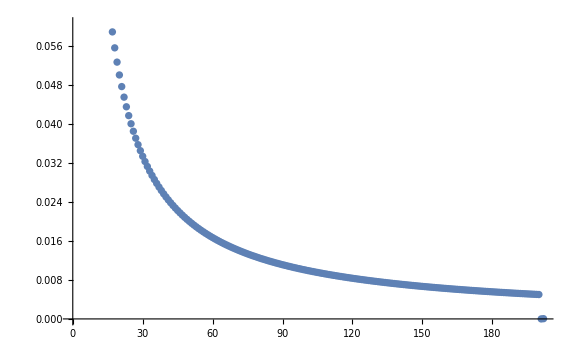

```mathematica
ListPlot[Flatten[{Table[1/n,{n,1,200}],0,1/20000}], ColorFunction->Function[{x},ColorData["Rainbow"][1-x^0.3]], ColorFunctionScaling->True, ImageSize->Large,FrameTicks->Automatic]
```

```mathematica
n=1;{Function[{x},ColorData["Rainbow"][1-#^0.3]],n++}&/@Flatten[{Table[1/n,{n,1,200}],0,1/20000}]
```

{{Function[{x},ColorData[Rainbow][1-1^0.3]],1},{Function[{x},ColorData[Rainbow][1-(1/2)^0.3]],2},{Function[{x},ColorData[Rainbow][1-(1/3)^0.3]],3},{Function[{x},ColorData[Rainbow][1-(1/4)^0.3]],4},{Function[{x},ColorData[Rainbow][1-(1/5)^0.3]],5},{Function[{x},ColorData[Rainbow][1-(1/6)^0.3]],6},{Function[{x},ColorData[Rainbow][1-(1/7)^0.3]],7},{Function[{x},ColorData[Rainbow][1-(1/8)^0.3]],8},{Function[{x},ColorData[Rainbow][1-(1/9)^0.3]],9},{Function[{x},ColorData[Rainbow][1-(1/10)^0.3]],10},{Function[{x},ColorData[Rainbow][1-(1/11)^0.3]],11},{Function[{x},ColorData[Rainbow][1-(1/12)^0.3]],12},{Function[{x},ColorData[Rainbow][1-(1/13)^0.3]],13},{Function[{x},ColorData[Rainbow][1-(1/14)^0.3]],14},{Function[{x},ColorData[Rainbow][1-(1/15)^0.3]],15},{Function[{x},ColorData[Rainbow][1-(1/16)^0.3]],16},{Function[{x},ColorData[Rainbow][1-(1/17)^0.3]],17},{Function[{x},ColorData[Rainbow][1-(1/18)^0.3]],18},{Function[{x},ColorData[Rainbow][1-(1/19)^0.3]],19},{Function[{x},ColorData[Rainbow][1-(1/20)^0.3]],20},{Function[{x},ColorData[Rainbow][1-(1/21)^0.3]],21},{Function[{x},ColorData[Rainbow][1-(1/22)^0.3]],22},{Function[{x},ColorData[Rainbow][1-(1/23)^0.3]],23},{Function[{x},ColorData[Rainbow][1-(1/24)^0.3]],24},{Function[{x},ColorData[Rainbow][1-(1/25)^0.3]],25},{Function[{x},ColorData[Rainbow][1-(1/26)^0.3]],26},{Function[{x},ColorData[Rainbow][1-(1/27)^0.3]],27},{Function[{x},ColorData[Rainbow][1-(1/28)^0.3]],28},{Function[{x},ColorData[Rainbow][1-(1/29)^0.3]],29},{Function[{x},ColorData[Rainbow][1-(1/30)^0.3]],30},{Function[{x},ColorData[Rainbow][1-(1/31)^0.3]],31},{Function[{x},ColorData[Rainbow][1-(1/32)^0.3]],32},{Function[{x},ColorData[Rainbow][1-(1/33)^0.3]],33},{Function[{x},ColorData[Rainbow][1-(1/34)^0.3]],34},{Function[{x},ColorData[Rainbow][1-(1/35)^0.3]],35},{Function[{x},ColorData[Rainbow][1-(1/36)^0.3]],36},{Function[{x},ColorData[Rainbow][1-(1/37)^0.3]],37},{Function[{x},ColorData[Rainbow][1-(1/38)^0.3]],38},{Function[{x},ColorData[Rainbow][1-(1/39)^0.3]],39},{Function[{x},ColorData[Rainbow][1-(1/40)^0.3]],40},{Function[{x},ColorData[Rainbow][1-(1/41)^0.3]],41},{Function[{x},ColorData[Rainbow][1-(1/42)^0.3]],42},{Function[{x},ColorData[Rainbow][1-(1/43)^0.3]],43},{Function[{x},ColorData[Rainbow][1-(1/44)^0.3]],44},{Function[{x},ColorData[Rainbow][1-(1/45)^0.3]],45},{Function[{x},ColorData[Rainbow][1-(1/46)^0.3]],46},{Function[{x},ColorData[Rainbow][1-(1/47)^0.3]],47},{Function[{x},ColorData[Rainbow][1-(1/48)^0.3]],48},{Function[{x},ColorData[Rainbow][1-(1/49)^0.3]],49},{Function[{x},ColorData[Rainbow][1-(1/50)^0.3]],50},{Function[{x},ColorData[Rainbow][1-(1/51)^0.3]],51},{Function[{x},ColorData[Rainbow][1-(1/52)^0.3]],52},{Function[{x},ColorData[Rainbow][1-(1/53)^0.3]],53},{Function[{x},ColorData[Rainbow][1-(1/54)^0.3]],54},{Function[{x},ColorData[Rainbow][1-(1/55)^0.3]],55},{Function[{x},ColorData[Rainbow][1-(1/56)^0.3]],56},{Function[{x},ColorData[Rainbow][1-(1/57)^0.3]],57},{Function[{x},ColorData[Rainbow][1-(1/58)^0.3]],58},{Function[{x},ColorData[Rainbow][1-(1/59)^0.3]],59},{Function[{x},ColorData[Rainbow][1-(1/60)^0.3]],60},{Function[{x},ColorData[Rainbow][1-(1/61)^0.3]],61},{Function[{x},ColorData[Rainbow][1-(1/62)^0.3]],62},{Function[{x},ColorData[Rainbow][1-(1/63)^0.3]],63},{Function[{x},ColorData[Rainbow][1-(1/64)^0.3]],64},{Function[{x},ColorData[Rainbow][1-(1/65)^0.3]],65},{Function[{x},ColorData[Rainbow][1-(1/66)^0.3]],66},{Function[{x},ColorData[Rainbow][1-(1/67)^0.3]],67},{Function[{x},ColorData[Rainbow][1-(1/68)^0.3]],68},{Function[{x},ColorData[Rainbow][1-(1/69)^0.3]],69},{Function[{x},ColorData[Rainbow][1-(1/70)^0.3]],70},{Function[{x},ColorData[Rainbow][1-(1/71)^0.3]],71},{Function[{x},ColorData[Rainbow][1-(1/72)^0.3]],72},{Function[{x},ColorData[Rainbow][1-(1/73)^0.3]],73},{Function[{x},ColorData[Rainbow][1-(1/74)^0.3]],74},{Function[{x},ColorData[Rainbow][1-(1/75)^0.3]],75},{Function[{x},ColorData[Rainbow][1-(1/76)^0.3]],76},{Function[{x},ColorData[Rainbow][1-(1/77)^0.3]],77},{Function[{x},ColorData[Rainbow][1-(1/78)^0.3]],78},{Function[{x},ColorData[Rainbow][1-(1/79)^0.3]],79},{Function[{x},ColorData[Rainbow][1-(1/80)^0.3]],80},{Function[{x},ColorData[Rainbow][1-(1/81)^0.3]],81},{Function[{x},ColorData[Rainbow][1-(1/82)^0.3]],82},{Function[{x},ColorData[Rainbow][1-(1/83)^0.3]],83},{Function[{x},ColorData[Rainbow][1-(1/84)^0.3]],84},{Function[{x},ColorData[Rainbow][1-(1/85)^0.3]],85},{Function[{x},ColorData[Rainbow][1-(1/86)^0.3]],86},{Function[{x},ColorData[Rainbow][1-(1/87)^0.3]],87},{Function[{x},ColorData[Rainbow][1-(1/88)^0.3]],88},{Function[{x},ColorData[Rainbow][1-(1/89)^0.3]],89},{Function[{x},ColorData[Rainbow][1-(1/90)^0.3]],90},{Function[{x},ColorData[Rainbow][1-(1/91)^0.3]],91},{Function[{x},ColorData[Rainbow][1-(1/92)^0.3]],92},{Function[{x},ColorData[Rainbow][1-(1/93)^0.3]],93},{Function[{x},ColorData[Rainbow][1-(1/94)^0.3]],94},{Function[{x},ColorData[Rainbow][1-(1/95)^0.3]],95},{Function[{x},ColorData[Rainbow][1-(1/96)^0.3]],96},{Function[{x},ColorData[Rainbow][1-(1/97)^0.3]],97},{Function[{x},ColorData[Rainbow][1-(1/98)^0.3]],98},{Function[{x},ColorData[Rainbow][1-(1/99)^0.3]],99},{Function[{x},ColorData[Rainbow][1-(1/100)^0.3]],100},{Function[{x},ColorData[Rainbow][1-(1/101)^0.3]],101},{Function[{x},ColorData[Rainbow][1-(1/102)^0.3]],102},{Function[{x},ColorData[Rainbow][1-(1/103)^0.3]],103},{Function[{x},ColorData[Rainbow][1-(1/104)^0.3]],104},{Function[{x},ColorData[Rainbow][1-(1/105)^0.3]],105},{Function[{x},ColorData[Rainbow][1-(1/106)^0.3]],106},{Function[{x},ColorData[Rainbow][1-(1/107)^0.3]],107},{Function[{x},ColorData[Rainbow][1-(1/108)^0.3]],108},{Function[{x},ColorData[Rainbow][1-(1/109)^0.3]],109},{Function[{x},ColorData[Rainbow][1-(1/110)^0.3]],110},{Function[{x},ColorData[Rainbow][1-(1/111)^0.3]],111},{Function[{x},ColorData[Rainbow][1-(1/112)^0.3]],112},{Function[{x},ColorData[Rainbow][1-(1/113)^0.3]],113},{Function[{x},ColorData[Rainbow][1-(1/114)^0.3]],114},{Function[{x},ColorData[Rainbow][1-(1/115)^0.3]],115},{Function[{x},ColorData[Rainbow][1-(1/116)^0.3]],116},{Function[{x},ColorData[Rainbow][1-(1/117)^0.3]],117},{Function[{x},ColorData[Rainbow][1-(1/118)^0.3]],118},{Function[{x},ColorData[Rainbow][1-(1/119)^0.3]],119},{Function[{x},ColorData[Rainbow][1-(1/120)^0.3]],120},{Function[{x},ColorData[Rainbow][1-(1/121)^0.3]],121},{Function[{x},ColorData[Rainbow][1-(1/122)^0.3]],122},{Function[{x},ColorData[Rainbow][1-(1/123)^0.3]],123},{Function[{x},ColorData[Rainbow][1-(1/124)^0.3]],124},{Function[{x},ColorData[Rainbow][1-(1/125)^0.3]],125},{Function[{x},ColorData[Rainbow][1-(1/126)^0.3]],126},{Function[{x},ColorData[Rainbow][1-(1/127)^0.3]],127},{Function[{x},ColorData[Rainbow][1-(1/128)^0.3]],128},{Function[{x},ColorData[Rainbow][1-(1/129)^0.3]],129},{Function[{x},ColorData[Rainbow][1-(1/130)^0.3]],130},{Function[{x},ColorData[Rainbow][1-(1/131)^0.3]],131},{Function[{x},ColorData[Rainbow][1-(1/132)^0.3]],132},{Function[{x},ColorData[Rainbow][1-(1/133)^0.3]],133},{Function[{x},ColorData[Rainbow][1-(1/134)^0.3]],134},{Function[{x},ColorData[Rainbow][1-(1/135)^0.3]],135},{Function[{x},ColorData[Rainbow][1-(1/136)^0.3]],136},{Function[{x},ColorData[Rainbow][1-(1/137)^0.3]],137},{Function[{x},ColorData[Rainbow][1-(1/138)^0.3]],138},{Function[{x},ColorData[Rainbow][1-(1/139)^0.3]],139},{Function[{x},ColorData[Rainbow][1-(1/140)^0.3]],140},{Function[{x},ColorData[Rainbow][1-(1/141)^0.3]],141},{Function[{x},ColorData[Rainbow][1-(1/142)^0.3]],142},{Function[{x},ColorData[Rainbow][1-(1/143)^0.3]],143},{Function[{x},ColorData[Rainbow][1-(1/144)^0.3]],144},{Function[{x},ColorData[Rainbow][1-(1/145)^0.3]],145},{Function[{x},ColorData[Rainbow][1-(1/146)^0.3]],146},{Function[{x},ColorData[Rainbow][1-(1/147)^0.3]],147},{Function[{x},ColorData[Rainbow][1-(1/148)^0.3]],148},{Function[{x},ColorData[Rainbow][1-(1/149)^0.3]],149},{Function[{x},ColorData[Rainbow][1-(1/150)^0.3]],150},{Function[{x},ColorData[Rainbow][1-(1/151)^0.3]],151},{Function[{x},ColorData[Rainbow][1-(1/152)^0.3]],152},{Function[{x},ColorData[Rainbow][1-(1/153)^0.3]],153},{Function[{x},ColorData[Rainbow][1-(1/154)^0.3]],154},{Function[{x},ColorData[Rainbow][1-(1/155)^0.3]],155},{Function[{x},ColorData[Rainbow][1-(1/156)^0.3]],156},{Function[{x},ColorData[Rainbow][1-(1/157)^0.3]],157},{Function[{x},ColorData[Rainbow][1-(1/158)^0.3]],158},{Function[{x},ColorData[Rainbow][1-(1/159)^0.3]],159},{Function[{x},ColorData[Rainbow][1-(1/160)^0.3]],160},{Function[{x},ColorData[Rainbow][1-(1/161)^0.3]],161},{Function[{x},ColorData[Rainbow][1-(1/162)^0.3]],162},{Function[{x},ColorData[Rainbow][1-(1/163)^0.3]],163},{Function[{x},ColorData[Rainbow][1-(1/164)^0.3]],164},{Function[{x},ColorData[Rainbow][1-(1/165)^0.3]],165},{Function[{x},ColorData[Rainbow][1-(1/166)^0.3]],166},{Function[{x},ColorData[Rainbow][1-(1/167)^0.3]],167},{Function[{x},ColorData[Rainbow][1-(1/168)^0.3]],168},{Function[{x},ColorData[Rainbow][1-(1/169)^0.3]],169},{Function[{x},ColorData[Rainbow][1-(1/170)^0.3]],170},{Function[{x},ColorData[Rainbow][1-(1/171)^0.3]],171},{Function[{x},ColorData[Rainbow][1-(1/172)^0.3]],172},{Function[{x},ColorData[Rainbow][1-(1/173)^0.3]],173},{Function[{x},ColorData[Rainbow][1-(1/174)^0.3]],174},{Function[{x},ColorData[Rainbow][1-(1/175)^0.3]],175},{Function[{x},ColorData[Rainbow][1-(1/176)^0.3]],176},{Function[{x},ColorData[Rainbow][1-(1/177)^0.3]],177},{Function[{x},ColorData[Rainbow][1-(1/178)^0.3]],178},{Function[{x},ColorData[Rainbow][1-(1/179)^0.3]],179},{Function[{x},ColorData[Rainbow][1-(1/180)^0.3]],180},{Function[{x},ColorData[Rainbow][1-(1/181)^0.3]],181},{Function[{x},ColorData[Rainbow][1-(1/182)^0.3]],182},{Function[{x},ColorData[Rainbow][1-(1/183)^0.3]],183},{Function[{x},ColorData[Rainbow][1-(1/184)^0.3]],184},{Function[{x},ColorData[Rainbow][1-(1/185)^0.3]],185},{Function[{x},ColorData[Rainbow][1-(1/186)^0.3]],186},{Function[{x},ColorData[Rainbow][1-(1/187)^0.3]],187},{Function[{x},ColorData[Rainbow][1-(1/188)^0.3]],188},{Function[{x},ColorData[Rainbow][1-(1/189)^0.3]],189},{Function[{x},ColorData[Rainbow][1-(1/190)^0.3]],190},{Function[{x},ColorData[Rainbow][1-(1/191)^0.3]],191},{Function[{x},ColorData[Rainbow][1-(1/192)^0.3]],192},{Function[{x},ColorData[Rainbow][1-(1/193)^0.3]],193},{Function[{x},ColorData[Rainbow][1-(1/194)^0.3]],194},{Function[{x},ColorData[Rainbow][1-(1/195)^0.3]],195},{Function[{x},ColorData[Rainbow][1-(1/196)^0.3]],196},{Function[{x},ColorData[Rainbow][1-(1/197)^0.3]],197},{Function[{x},ColorData[Rainbow][1-(1/198)^0.3]],198},{Function[{x},ColorData[Rainbow][1-(1/199)^0.3]],199},{Function[{x},ColorData[Rainbow][1-(1/200)^0.3]],200},{Function[{x},ColorData[Rainbow][1-0^0.3]],201},{Function[{x},ColorData[Rainbow][1-(1/20000)^0.3]],202}}

```mathematica
Function[{x},ColorData["Rainbow"][1-x^0.3]]
```

```mathematica
RGBColor[0.52,0.92,0.]
```

```mathematica
RGBColor[0.24, 0.92, 0.]
```

```mathematica
RGBColor[0.91,0.9,0.24]
```

RGBColor[0.91, 0.9, 0.24]

```mathematica
Floor @ComplexInfinity
```

ComplexInfinity

```mathematica
{RGBColor[1.,0.09,0.04],RGBColor[0.52,0.92,0.]
```

```mathematica
{RGBColor[1.,0.49,0.27],1}
```

```mathematica
{RGBColor[0.03, 0.35000000000000003, 0.],1}
```

```mathematica
Manipulate[Magnify@myblend[If[x>0,1/x,x]],{x,0,200} ]
```

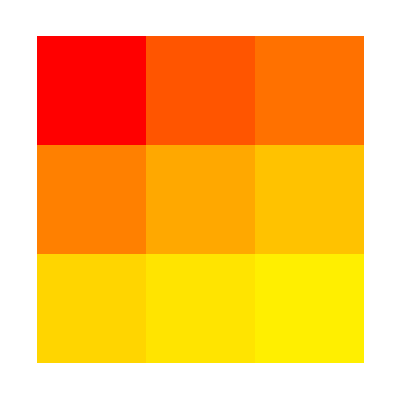

```mathematica
ArrayPlot[{{1,2,3},{4,5,6},{7,8,9}},ColorFunction->Function[{x},myblend[If[x>0,1/x,0]]],ColorFunctionScaling->False]
```

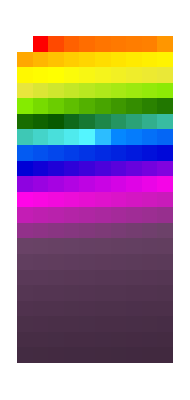

```mathematica
ArrayPlot[Table[10i+j,{i,0,20},{j,0,9}],ColorFunction->Function[{x},myblend[If[x>0,1/x,0]]],ColorFunctionScaling->False]
```